## Problem 1

```mathematica
Integrate[Exp[-4Z x/a]/(4Z^3)(-2Z^5 a x^3 - 2 Z^4 a^2 x^2 - Z^3 a^3 x - 2 Z^2 a x^3 + Z a^2 x^2),{x,0,Infinity}]
```

ConditionalExpression[-(a^5 (-5+11 Z^3))/(256 Z^5),(Re[a]≠0||a∉Reals)&&Re[Z/a]>0]

```mathematica
-(a^5 (-5+11 Z^3))/(256 Z^5)16π^2e^2//FullSimplify
```

(a^5 e^2 π^2 (5-11 Z^3))/(16 Z^5)

```mathematica
Integrate[Exp[-2Z x/a]x^2,{x,0,r1}]r1+Integrate[Exp[-2Z x/a]x,{x,r1,Infinity},Assumptions->Re[Z/a]>0]r1^2
```

(a ⅇ^(-(2 r1 Z)/a) r1^2 (a+2 r1 Z))/(4 Z^2)+(a r1 (a^2-ⅇ^(-(2 r1 Z)/a) (a^2+2 a r1 Z+2 r1^2 Z^2)))/(4 Z^3)

```mathematica
Integrate[((a ⅇ^(-(2 r1 Z)/a) r1^2 (a+2 r1 Z))/(4 Z^2)+(a r1 (a^2-ⅇ^(-(2 r1 Z)/a) (a^2+2 a r1 Z+2 r1^2 Z^2)))/(4 Z^3))Exp[-2Z r1/a],{r1,0,Infinity},Assumptions->ConditionalExpression[(5 a^5 e^2 π^2)/(8 Z^5),Re[Z/a]>0]]16 π^2 e^2
```

(5 a^5 e^2 π^2)/(8 Z^5)

```mathematica
N[(27/16)^2] *2 13.6
```

77.4563

## Problem 2

```mathematica
Integrate[Exp[-a x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√a),Re[a]>0]

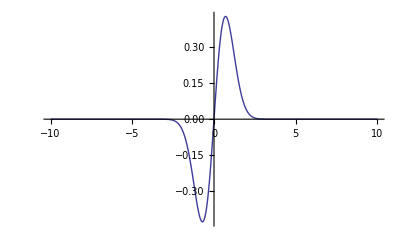

```mathematica
Plot[Exp[-x^2]x,{x,-10,10},PlotRange->Full]
```

```mathematica
D[x Exp[-a x^2/2],x]
D[x Exp[-a x^2/2],x]^2
```

ⅇ^(-(a x^2)/2)-a ⅇ^(-(a x^2)/2) x^2

(ⅇ^(-(a x^2)/2)-a ⅇ^(-(a x^2)/2) x^2)^2

```mathematica
Integrate[D[x Exp[-a x^2/2],x]^2,{x,-Infinity,Infinity}]
```

ConditionalExpression[(3 √π)/(4 √a),Re[a]>0]

```mathematica
Integrate[x^2 Exp[-a x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(2 a^(3/2)),Re[a]>0]

```mathematica
Integrate[x^4 Exp[-a x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(3 √π)/(4 a^(5/2)),Re[a]>0]